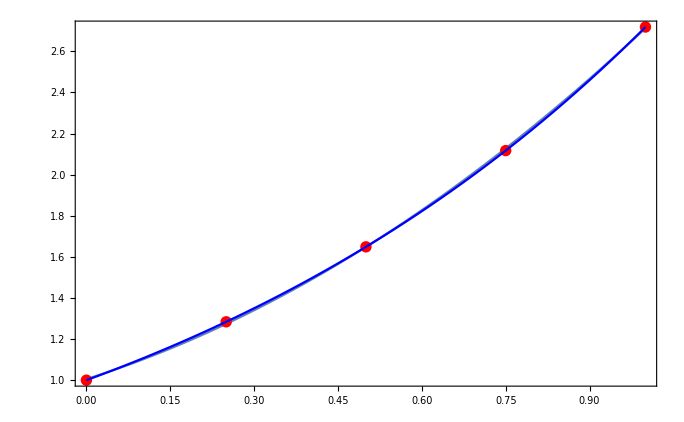

0.000274133

```mathematica
xi={0.,0.25,0.50,0.75,1.00};
fi={1.0000,1.2840,1.6487,2.1170,2.7183};
m=Length[xi];
n=2;
A=Table[∑_(i=1)^m If[k-1+j-1==0,1,xi[[i]]^(k-1+j-1)],{k,1,n+1},{j,1,n+1}];
α=Table[a[i-1],{i,1,n+1}];
b=Table[∑_(i=1)^m fi[[i]] If[k-1==0,1,xi[[i]]^(k-1)],{k,1,n+1}];
α=α/.Solve[A.α==b,α][[1]];
p[x_]:=α.Table[If[i-1==0,1,x^(i-1)],{i,1,n+1}];
L[j_Integer,x_]:=(∏_(k=0)^(j-1) (x-xi[[k+1]])/(xi[[j+1]]-xi[[k+1]])) (∏_(k=j+1)^(m-1) (x-xi[[k+1]])/(xi[[j+1]]-xi[[k+1]]));
ip[x_]:=∑_(j=0)^(m-1) fi[[j+1]] L[j,x];
p1=Plot[p[x],{x,xi[[1]],xi[[m]]},DisplayFunction->Identity];
p2=ListPlot[Table[{xi[[i]],fi[[i]]},{i,1,m}],PlotStyle->{RGBColor[1,0,0],PointSize[0.012]},DisplayFunction->Identity];
p3=Plot[ip[x],{x,xi[[1]],xi[[m]]},DisplayFunction->Identity,PlotStyle->RGBColor[0,0,1]];
Show[p1,p2,p3,DisplayFunction->$DisplayFunction,Frame->True]
E2=∑_(i=1)^m (fi[[i]]-p[xi[[i]]])^2
```